```mathematica
ClearAll["Global`*"]
```

```mathematica
$Assumptions={θ<π/2, θ>-π/2,d>0,ϵ>0,h>d, h>0};
```

```mathematica
(*df[ζ_]=k(∏_(j=-∞)^∞ (1+d^2/(ζ+2ⅈ j h)^2))^(θ/π)*)
```

```mathematica
df[ζ_]=(1+Csch[(π ζ)/(2 h)]^2 Sin[(d π)/(2 h)]^2)^(θ/π);
```

```mathematica
Block[{d=1.2,h=1.8,θ =20*π/180,ζ=.47-.48ⅈ},{(∏_(j=-5)^5 (1+d^2/(ζ+2ⅈ j h)^2))^(θ/π),df[ζ]}]
```

{1.08992+0.153116 ⅈ,1.08505+0.152426 ⅈ}

```mathematica
(*Limit[df[ζ],h->∞] should return (1+d^2/ζ^2)^(θ/π)*)
```

```mathematica
(*f[ζ_]=∫(df[ζ]/.θ->π/4)ⅆζ+c has an uglu AppellF1-type solution *)
```

```mathematica
df[ⅈ σ]//Simplify
```

(1-Csc[(π σ)/(2 h)]^2 Sin[(d π)/(2 h)]^2)^(θ/π)

```mathematica
df[-ⅈ h]
```

(1-Sin[(d π)/(2 h)]^2)^(θ/π)

```mathematica
df[-ⅈ d]
```

0^(θ/π)

```mathematica
Limit[df[ⅈ σ],σ->-d]
```

Limit[(1-Csc[(π σ)/(2 h)]^2 Sin[(d π)/(2 h)]^2)^(θ/π),σ→-d]

```mathematica
∫_(-π/2)^-d (1-(Sin[d]/Sin[σ])^2)^(θ/π)ⅆσ
```

∫_(-π/2)^-d (1-Csc[σ]^2 Sin[d]^2)^(θ/π)ⅆσ

```mathematica
Block[{d=1.6,h=3,θ=30*π/180},df[-ⅈ h]]
```

0.874655 k

```mathematica
Block[{d=1.6,h=3,θ=30*π/180},NIntegrate[(1-(Sin[π d/(2h)]/Sin[π σ/(2h)])^2)^(θ/π)/h,{σ,-h,-d}]]
```

0.378632

```mathematica
Block[{td=π/2* 1.6/3,θ=30*π/180},2/π NIntegrate[(1-(Sin[td]/Sin[σ])^2)^(θ/π),{σ,-π/2,-td}]]
```

0.378632

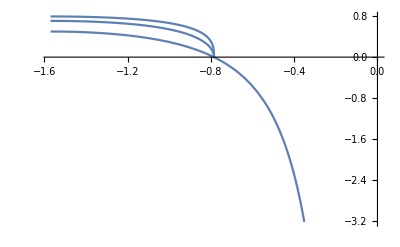

```mathematica
Block[{d=π/4},Plot[Table[(1-(Sin[d]/Sin[σ])^2)^((π/i)/π),{i,1,3}],{σ,-π/2,-0}]]
```

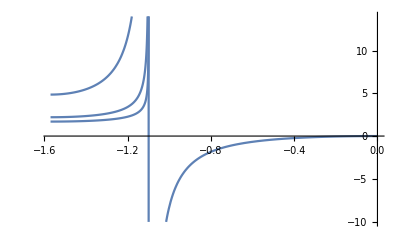

```mathematica
Block[{d=.35π},Plot[Table[(1-(Sin[d]/Sin[σ])^2)^((π/i)/π),{i,-3,-1}],{σ,-π/2,0}]]
```

```mathematica
c=-(dz+du) Tan[θ]+ⅈ du;
d= (√π(du+dz) Sec[θ])/(Gamma[1+θ/π] Gamma[1/2-θ/π]);
```

```mathematica
Block[{dz=.6,du = .0,h=2d,θ =20*π/180,lim={.00001,5,-1.2,1.2}},
Show[ParametricPlot[Array[ReIm@f[ξ+ⅈ #]&,6,lim⟦{3,4}⟧],{ξ,lim⟦1⟧,lim⟦2⟧},PlotStyle->{Blue},AspectRatio->Automatic],
 ParametricPlot[Array[ReIm@f[#+ⅈ η]&,8,lim⟦{1,2}⟧],{η,lim⟦3⟧,lim⟦4⟧},PlotStyle->{Red},AspectRatio->Automatic]]]
```

$Aborted